```mathematica
data=Import["~/Documents/work/tutors/CESAM/cours/Stata/birthwt2.csv"];
dt=data[[2;;,{2,1}]];
m=GeneralizedLinearModelFit[dt,x,x,ExponentialFamily->"Binomial"];
```

```mathematica
m//Normal
```

1/(1+ⅇ^(-0.384582+0.0511529 x))

```mathematica
ecdf=EmpiricalDistribution[dt[[All,1]]];
f[x_]:=1+CDF[ecdf,x] 10//Floor
qvalues=Map[f,dt[[All,1]]];
qvalues=qvalues /.{11->10};
```

```mathematica
tens=Quantile[dt[[All,1]],Range[0,1,.1]];
centers=Total[{Most[tens],Differences[tens]/2}]
```

{31/2,18,39/2,41/2,22,47/2,49/2,53/2,59/2,38}

```mathematica
SetAttributes[g,Listable]
```

```mathematica
g[a_,b_]:=a->b
```

```mathematica
dt=MapThread[Append,{dt,qvalues /. g[Table[x,{x,10}],centers]}];
```

```mathematica
obs=GroupBy[Sort[dt[[All,2;;]]], Last->First, Mean]
```

<|31/2→5/13,18→7/22,39/2→3/16,41/2→4/9,22→7/25,47/2→5/13,49/2→5/13,53/2→6/13,59/2→4/23,38→3/20|>

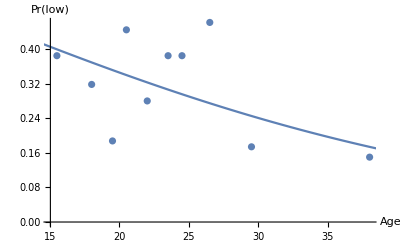

```mathematica
Show[ListPlot[obs],Plot[m[x],{x,14,45}], AxesLabel->{"Age", "Pr(low)"}]
```

```mathematica
Export["birthwt_glm.png", %, ImageResolution->300]
```

birthwt_glm.png